```mathematica
pde=D[u[x,t],t]+(x+E^t)D[u[x,t],x]==x(x+E^t);
sol=DSolve[{pde,u[0,t]==-t},u[x,t],{x,t}]
analyticPlot=Plot3D[u[x,t]/.sol,{x,-1,1},{t,-1,1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u[x,t]→-1/2 ⅇ^-t (2 ⅇ^t t-2 x-ⅇ^t x^2)}}

-Graphics3D-

```mathematica
AnalyticEval[x_,t_]:=N[-1/2 ⅇ^-t (2 ⅇ^t t-2 x-ⅇ^t x^2)];
L=10;
trail=Table[AnalyticEval[x,1],{x,0,1,1/L}]
```

{-1.,-0.958212,-0.906424,-0.844636,-0.772848,-0.69106,-0.599272,-0.497484,-0.385696,-0.263909,-0.132121}

```mathematica
AnalyticNet=Table[AnalyticEval[x,t],{t,0,1,1/L},{x,0,1,1/L}];
TableForm[AnalyticNet]
```

0. | 0.105 | 0.22 | 0.345 | 0.48 | 0.625 | 0.78 | 0.945 | 1.12 | 1.305 | 1.5
-0.1 | -0.00451626 | 0.100967 | 0.216451 | 0.341935 | 0.477419 | 0.622902 | 0.778386 | 0.94387 | 1.11935 | 1.30484
-0.2 | -0.113127 | -0.0162538 | 0.0906192 | 0.207492 | 0.334365 | 0.471238 | 0.618112 | 0.774985 | 0.941858 | 1.11873
-0.3 | -0.220918 | -0.131836 | -0.0327545 | 0.0763273 | 0.195409 | 0.324491 | 0.463573 | 0.612655 | 0.771736 | 0.940818
-0.4 | -0.327968 | -0.245936 | -0.153904 | -0.051872 | 0.06016 | 0.182192 | 0.314224 | 0.456256 | 0.608288 | 0.77032
-0.5 | -0.434347 | -0.358694 | -0.273041 | -0.177388 | -0.0717347 | 0.0439184 | 0.169571 | 0.305225 | 0.450878 | 0.606531
-0.6 | -0.540119 | -0.470238 | -0.390357 | -0.300475 | -0.200594 | -0.090713 | 0.0291681 | 0.159049 | 0.29893 | 0.448812
-0.7 | -0.645341 | -0.580683 | -0.506024 | -0.421366 | -0.326707 | -0.222049 | -0.10739 | 0.0172682 | 0.151927 | 0.296585
-0.8 | -0.750067 | -0.690134 | -0.620201 | -0.540268 | -0.450336 | -0.350403 | -0.24047 | -0.120537 | 0.00939607 | 0.149329
-0.9 | -0.854343 | -0.798686 | -0.733029 | -0.657372 | -0.571715 | -0.476058 | -0.370401 | -0.254744 | -0.129087 | 0.00656966
-1. | -0.958212 | -0.906424 | -0.844636 | -0.772848 | -0.69106 | -0.599272 | -0.497484 | -0.385696 | -0.263909 | -0.132121

```mathematica
ListPlot3D[AnalyticNet]
```

-Graphics3D-

```mathematica
ClearAll[numerical]
h=1/L;
k=1;
τ=h*k;
Nm=Round[1/τ];
T=0;
dt=k*h;
dtx=dt/h;
numerical=Table[0,{x,L+1}];
For[l=1,l<=L+1,l++,
numerical[[l]]=N[1/L*(l-1)+0.5*(1/L*(l-1))^2];
]
MatrixForm[numerical]
```

(0.
0.105
0.22
0.345
0.48
0.625
0.78
0.945
1.12
1.305
1.5)

```mathematica
While[T+dt<1.0,
For[l=10,l≥ 4,l--,
numerical[[l+1]]=N[numerical[[l]]+dtx/(6h)(Exp[T]-dtx/2(1-dtx/3)*(1/L*l)+(1/L*l))*(2numerical[[l-3]]-9numerical[[l-2]]+18numerical[[l-1]]-11numerical[[l]])+dtx^2/(2 h^2)((l/L)+Exp[T])(l/L+Exp[T]-dtx*l/L)(-numerical[[l-3]]+4numerical[[l-2]]-5numerical[[l-1]]+2numerical[[l]])-(dtx^3(l/L+Exp[T])^3)/(6 h^3)(-numerical[[l-3]]+3numerical[[l-2]]-3numerical[[l-1]]+numerical[[l]])+dtx(l/L(l/L+Exp[T])-dtx/2(Exp[2T]+2 l/L*Exp[T]+2(l/L)^2)+(dtx^2 l/L)/6*(4 l/L+3Exp[T]))];
];
T+=dt;
numerical[[3]] = N[-T+2*Exp[-T]*h+2*h^2];
 numerical[[2]] =  N[-T+Exp[-T]*h+h^2/2];
numerical[[1]]=N[-T];
dt=k*h/Exp[T];
dtx=dt/h;
 ]
dt=1-T;
dtx=dt/h;
MatrixForm[numerical]
```

Part::partd: Part specification {0.,0.105,0.22,0.345,0.48,0.625,0.78,0.945,1.12,1.305,1.5}⟦4,12⟧ is longer than depth of object.

Part::partd: Part specification {0.,0.105,0.22,0.345,0.48,0.625,0.78,0.945,1.12,1.305,1.5}⟦4,9⟧ is longer than depth of object.

Part::partd: Part specification {0.,0.105,0.22,0.345,0.48,0.625,0.78,0.945,1.12,1.305,1.5}⟦4,10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification numerical⟦n,l⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

Set::partw: Part 12 of {0.,0.105,0.22,0.345,0.48,0.625,0.78,0.945,1.12,1.305,1.5} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

```mathematica
dt=1-T;
dtx=dt/h;
```

```mathematica
For[n=Nm,n≤ Nm,n++,
For[l=4,l≤ L,l++,
numerical[[n+1,l]]=N[numerical[[n,l]]+dtx/(6h)(Exp[T]-dtx/2(1-dtx/3)*(1/L*l)+(1/L*l))*(2numerical[[n,l-3]]-9numerical[[n,l-2]]+18numerical[[n,l-1]]-11numerical[[n,l]])+dtx^2/(2 h^2)((l/L)+Exp[T])(l/L+Exp[T]-dtx*l/L)(-numerical[[n,l-3]]+4numerical[[n,l-2]]-5numerical[[n,l-1]]+2numerical[[n,l]])-(dtx^3(l/L+Exp[T])^3)/(6 h^3)(-numerical[[n,l-3]]+3numerical[[n,l-2]]-3numerical[[n,l-1]]+numerical[[n,l]])+dtx(l/L(l/L+Exp[T])-dtx/2(Exp[2T]+2 l/L*Exp[T]+2(l/L)^2)+(dtx^2 l/L)/6*(4 l/L+3Exp[T]))];
]
]
numerical[[Nm+1,3]] = N[-1+2*Exp[-1]*h+2*h^2];
 numerical[[Nm+1,2]] =  N[-1+Exp[-1]*h+h^2/2];
numerical[[Nm+1,1]]=-1;
MatrixForm[numerical]
```

(0. | 0.105 | 0.22 | 0.345 | 0.48 | 0.625 | 0.78 | 0.945 | 1.12 | 1.305 | 1.5
-0.1 | -0.00451626 | 0.100967 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.190484 | -0.102828 | -0.0051719 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.27314 | -0.192041 | -0.100942 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.349238 | -0.273716 | -0.188193 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.419761 | -0.34904 | -0.26832 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.485481 | -0.418941 | -0.342401 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.547021 | -0.484154 | -0.411287 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.604888 | -0.545275 | -0.475661 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.659502 | -0.602791 | -0.53608 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | -0.958212 | -0.906424 | -80.8821 | 222.9 | -156.176 | 0.101801 | 0.214081 | 0.332939 | 0.458373 | 0)

-Graphics3D-

-Graphics3D-

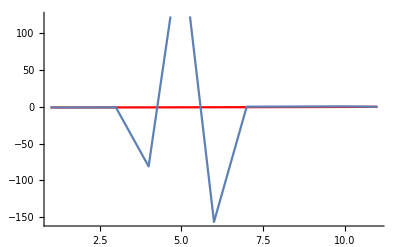

-1. | -0.958212 | -0.906424 | -0.844636 | -0.772848 | -0.69106 | -0.599272 | -0.497484 | -0.385696 | -0.263909 | -0.132121
-1. | -0.958212 | -0.906424 | -80.8821 | 222.9 | -156.176 | 0.101801 | 0.214081 | 0.332939 | 0.458373 | 0.

```mathematica
Plot3D[u[x,t]/.sol,{x,0,1},{t,0,1}]
ListPlot3D[numerical]
Show[ListLinePlot[trail,PlotStyle-> Red,PlotRange->{{0,12},{0,-1.2}}],ListLinePlot[numerical[[n,All]]]]
deltas=trail-numerical[[n,All]];
TableForm[{trail,N[numerical[[n,All]]]}]
```

```mathematica
CForm[numerical[[n,l]]+dtx/(6h)(Exp[T]-dtx/2(1-dtx/3)*(1/L*l)+(1/L*l))*(2numerical[[n,l-3]]-9numerical[[n,l-2]]+18numerical[[n,l-1]]-11numerical[[n,l]])+dtx^2/(2 h^2)((l/L)+Exp[T])(l/L+Exp[T]-dtx*l/L)(-numerical[[n,l-3]]+4numerical[[n,l-2]]-5numerical[[n,l-1]]+2numerical[[n,l]])-(dtx^3(l/L+Exp[T])^3)/(6 h^3)(-numerical[[n,l-3]]+3numerical[[n,l-2]]-3numerical[[n,l-1]]+numerical[[n,l]])+dtx(l/L(l/L+Exp[T])-dtx/2(Exp[2T]+2 l/L*Exp[T]+2(l/L)^2)+(dtx^2 l/L)/6*(4 l/L+3Exp[T]))]
```

Part::pkspec1: The expression n cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

dtx*(-(dtx*(Power(E,2*T) + (2*Power(l,2))/Power(L,2) + (2*Power(E,T)*l)/L))/2. + 
      (l*(Power(E,T) + l/L))/L + (Power(dtx,2)*l*(3*Power(E,T) + (4*l)/L))/(6.*L)) + 
   (dtx*(Power(E,T) + l/L - ((1 - dtx/3.)*dtx*l)/(2.*L))*
      (2*numerical[n][-3 + l] - 9*numerical[n][-2 + l] + 18*numerical[n][-1 + l] - 
        11*numerical[n][l]))/(6.*h) + numerical[n][l] - 
   (Power(dtx,3)*Power(Power(E,T) + l/L,3)*
      (-numerical[n][-3 + l] + 3*numerical[n][-2 + l] - 3*numerical[n][-1 + l] + numerical[n][l]))/
    (6.*Power(h,3)) + (Power(dtx,2)*(Power(E,T) + l/L)*(Power(E,T) + l/L - (dtx*l)/L)*
      (-numerical[n][-3 + l] + 4*numerical[n][-2 + l] - 5*numerical[n][-1 + l] + 2*numerical[n][l])
      )/(2.*Power(h,2))

```mathematica
LK+1-(LK-3)
```

4